```mathematica
Remove["Global`*"];
fd=((2/L)*(1-(d/L)));
fr =1/(P/2);
a = {w∈Reals,P∈Reals,L∈Reals,  w>0,w ≤ P/2 , L>0, P > 0, 2* L > P};
I1=FullSimplify[Integrate[Integrate[fd*fr,{d,0,Sqrt[w^2-r^2]}],{r,0,w}]];
D1=FullSimplify[Dt[I1,w,Constants -> {L, P}],a];
PDF1 = D1
CDF1 = I1
```

(2 (L π-2 w) w)/(L^2 P)

(-4 w^3+3 L π w √(w^2))/(3 L^2 P)

```mathematica
CForm[PDF1]
```

(2*(L*Pi - 2*w)*w)/(Power(L,2)*P)

```mathematica
CForm[CDF1]
```

(-4*Power(w,3) + 3*L*Pi*w*Sqrt(Power(w,2)))/(3.*Power(L,2)*P)

```mathematica
b = {w∈Reals,P∈Reals,L∈Reals,w>=(P/2),w ≤ L,  L > 0,P>0, 2* L > P, 2* w>P };
I2 =Apart[FullSimplify[Integrate[Integrate[fd*fr,{d,Sqrt[(P/2)^2-r^2],Sqrt[w^2-r^2]},Assumptions-> b],{r,0, (P/2)},Assumptions-> b],b]];

D2=Apart[FullSimplify[Dt[I2,w,Constants -> {L,P}],b]];
PDF2 = D2
CDF2 =  Apart[FullSimplify[I2+ Function[w, Evaluate[CDF1]][P/2], b]]
```

-(2 w)/L^2+(4 w ArcCsc[(2 w)/P])/(L P)

(P^2-12 w^2)/(12 L^2)+(√(-P^2+4 w^2))/(2 L)+(2 w^2 ArcCsc[(2 w)/P])/(L P)

```mathematica
CForm[PDF2]
```

(-2*w)/Power(L,2) + (4*w*ArcCsc((2*w)/P))/(L*P)

```mathematica
CForm[CDF2]
```

(Power(P,2) - 12*Power(w,2))/(12.*Power(L,2)) + 
   Sqrt(-Power(P,2) + 4*Power(w,2))/(2.*L) + 
   (2*Power(w,2)*ArcCsc((2*w)/P))/(L*P)

```mathematica
c = {w∈Reals,P∈Reals,L∈Reals,w>L,w < Sqrt[(P/2)^2 +L^2],2 * L> P,L>0, P> 0};
I3=Apart[FullSimplify[Integrate[Integrate[fd*fr,{r, 0, Sqrt[w^2 - d^2]},Assumptions ->c],{d, L, w},Assumptions ->c],c]];

D3=Apart[FullSimplify[Dt[I3,
   w, Constants -> {L,P}],{w∈Reals,P∈Reals,L∈Reals, w>L,L>(P/2),w>0}]];
PDF3 = Apart[FullSimplify[D2-D3]]
CDF3 = Apart[FullSimplify[I2-I3  +  1 - Function[w, Evaluate[I2 - I3]][Sqrt[(P/2)^2 + L^2]], {w>L,L>(P/2),w>0, P>0}]]
```

-(2 w)/L^2+(4 w √(-L^2+w^2))/(L^2 P)-(4 (w ArcCos[L/w]-w ArcCsc[(2 w)/P]))/(L P)

(P^2-12 w^2)/(12 L^2)+(2 √(-L^2+w^2))/(3 P)+(4 w^2 √(-L^2+w^2))/(3 L^2 P)+(√(-P^2+4 w^2))/(2 L)+(2 L (ArcCos[(2 L)/(√(4 L^2+P^2))]-ArcSin[P/(√(4 L^2+P^2))]))/P+(P^2 ArcCos[(2 L)/(√(4 L^2+P^2))]-4 w^2 ArcCos[L/w]+4 w^2 ArcCsc[(2 w)/P]-P^2 ArcSin[P/(√(4 L^2+P^2))])/(2 L P)

```mathematica
CForm[PDF3]
```

(-2*w)/Power(L,2) + (4*w*Sqrt(-Power(L,2) + Power(w,2)))/(Power(L,2)*P) - 
   (4*(w*ArcCos(L/w) - w*ArcCsc((2*w)/P)))/(L*P)

```mathematica
CForm[CDF3]
```

(Power(P,2) - 12*Power(w,2))/(12.*Power(L,2)) + 
   (2*Sqrt(-Power(L,2) + Power(w,2)))/(3.*P) + 
   (4*Power(w,2)*Sqrt(-Power(L,2) + Power(w,2)))/(3.*Power(L,2)*P) + 
   Sqrt(-Power(P,2) + 4*Power(w,2))/(2.*L) + 
   (2*L*(ArcCos((2*L)/Sqrt(4*Power(L,2) + Power(P,2))) - 
        ArcSin(P/Sqrt(4*Power(L,2) + Power(P,2)))))/P + 
   (Power(P,2)*ArcCos((2*L)/Sqrt(4*Power(L,2) + Power(P,2))) - 
      4*Power(w,2)*ArcCos(L/w) + 4*Power(w,2)*ArcCsc((2*w)/P) - 
      Power(P,2)*ArcSin(P/Sqrt(4*Power(L,2) + Power(P,2))))/(2.*L*P)

```mathematica
d = {w∈Reals,P∈Reals,L∈Reals,w>0, L > 0,  P> 0};
```

```mathematica
MOMENT1 = FullSimplify[Integrate [w * PDF1, {w, 0, P/2}, Assumptions->a] +
          Integrate [w * PDF2, {w, P/2, L}, Assumptions->b] +
         Integrate [w * PDF3, {w, L, Sqrt[(P/2)^2 + L^2]}, Assumptions->c],d]
```

1/(48 L^2 P √(4 L^2+P^2))(P^4 √(4 L^2+P^2)-4 L (4 L^2+P^2)^2 π+(4 L^2+P^2) (6 L^2 P-P^3+8 L (4 L^2+P^2) (ArcSin[(2 L)/(√(4 L^2+P^2))]+ArcSin[P/(√(4 L^2+P^2))]))+4 L P^3 √(4 L^2+P^2) Log[(2 L+√(4 L^2+P^2))/P]-L^4 √(4 L^2+P^2) Log[(256 L^8)/((P+√(4 L^2+P^2))^8)])

```mathematica
CForm[MOMENT1]
```

(Power(P,4)*Sqrt(4*Power(L,2) + Power(P,2)) - 
     4*L*Power(4*Power(L,2) + Power(P,2),2)*Pi + 
     (4*Power(L,2) + Power(P,2))*
      (6*Power(L,2)*P - Power(P,3) + 
        8*L*(4*Power(L,2) + Power(P,2))*
         (ArcSin((2*L)/Sqrt(4*Power(L,2) + Power(P,2))) + 
           ArcSin(P/Sqrt(4*Power(L,2) + Power(P,2))))) + 
     4*L*Power(P,3)*Sqrt(4*Power(L,2) + Power(P,2))*
      Log((2*L + Sqrt(4*Power(L,2) + Power(P,2)))/P) - 
     Power(L,4)*Sqrt(4*Power(L,2) + Power(P,2))*
      Log((256*Power(L,8))/Power(P + Sqrt(4*Power(L,2) + Power(P,2)),8)))/
   (48.*Power(L,2)*P*Sqrt(4*Power(L,2) + Power(P,2)))

```mathematica
MOMENT2= FullSimplify[Integrate [PDF1 * (w )^2, {w, 0, P/2}, Assumptions->a] +
                                  Integrate [PDF2 * (w )^2, {w, P/2, L}, Assumptions->b] +
Integrate [PDF3 *(w )^2, {w, L, Sqrt[(P/2)^2 + L^2]}, Assumptions->c] ,d] 
CForm[MOMENT2]
```

(8 L P (2 L^2+P^2)-3 (4 L^2+P^2)^2 π+6 (4 L^2+P^2)^2 (ArcSin[(2 L)/(√(4 L^2+P^2))]+ArcSin[P/(√(4 L^2+P^2))]))/(96 L P)

(8*L*P*(2*Power(L,2) + Power(P,2)) - 
     3*Power(4*Power(L,2) + Power(P,2),2)*Pi + 
     6*Power(4*Power(L,2) + Power(P,2),2)*
      (ArcSin((2*L)/Sqrt(4*Power(L,2) + Power(P,2))) + 
        ArcSin(P/Sqrt(4*Power(L,2) + Power(P,2)))))/(96.*L*P)

```mathematica
CForm[MOMENT2 - MOMENT1^2]
```

(8*L*P*(2*Power(L,2) + Power(P,2)) - 
      3*Power(4*Power(L,2) + Power(P,2),2)*Pi + 
      6*Power(4*Power(L,2) + Power(P,2),2)*
       (ArcSin((2*L)/Sqrt(4*Power(L,2) + Power(P,2))) + 
         ArcSin(P/Sqrt(4*Power(L,2) + Power(P,2)))))/(96.*L*P) - 
   Power(Power(P,4)*Sqrt(4*Power(L,2) + Power(P,2)) - 
      4*L*Power(4*Power(L,2) + Power(P,2),2)*Pi + 
      (4*Power(L,2) + Power(P,2))*
       (6*Power(L,2)*P - Power(P,3) + 
         8*L*(4*Power(L,2) + Power(P,2))*
          (ArcSin((2*L)/Sqrt(4*Power(L,2) + Power(P,2))) + 
            ArcSin(P/Sqrt(4*Power(L,2) + Power(P,2))))) + 
      4*L*Power(P,3)*Sqrt(4*Power(L,2) + Power(P,2))*
       Log((2*L + Sqrt(4*Power(L,2) + Power(P,2)))/P) - 
      Power(L,4)*Sqrt(4*Power(L,2) + Power(P,2))*
       Log((256*Power(L,8))/Power(P + Sqrt(4*Power(L,2) + Power(P,2)),8)),2)/
    (2304.*Power(L,4)*Power(P,2)*(4*Power(L,2) + Power(P,2)))

```mathematica
L=7
P=2*π
N[Integrate[D1,{w,0,(P/2)}]+ Integrate[D2,{w,P/2,L}]+Integrate[D2-D3,{w,L,Sqrt[L^2+(P/2)^2]}]]
```

7

2 π

1.

```mathematica
20
```

20

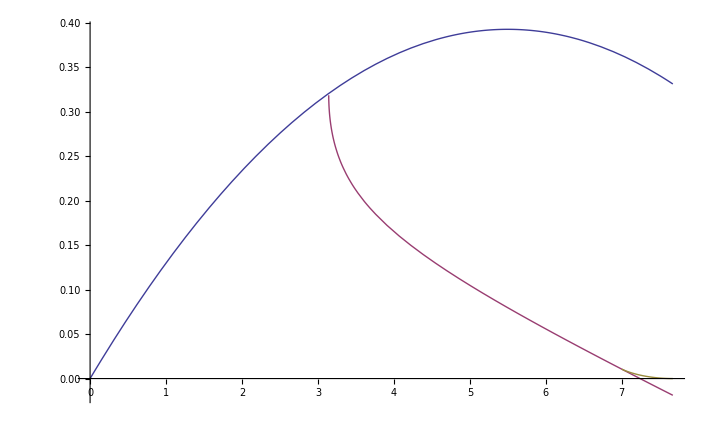

```mathematica
Plot[{PDF1,PDF2,PDF3,VAR},{w,0,Sqrt[L^2+π^2]}]
```

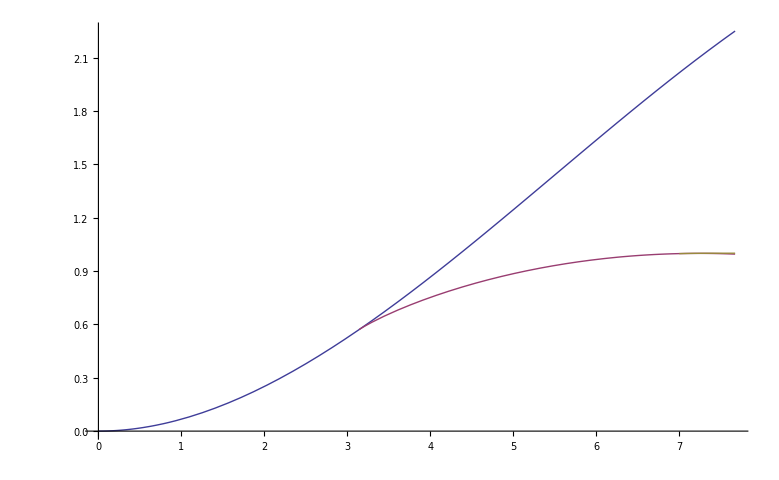

```mathematica
Plot[{CDF1,CDF2,CDF3},{w,0,Sqrt[L^2+π^2]}]
```